# A model to study the impact of government-imposed social distancing on COVID-19 epidemic in Portugal

## Clearing memory

```mathematica
ClearSystemCache[]
ClearAll["Global`*"]
Clear["Subscript"]
Clear["Superscript"]
Clear["Subsuperscript"]
```

## O estado de emergência: 18/03/2020, 17th day after 02/03/2020 (date of first confirmed cases in Portugal) O dia de hoje: 25/03/2020, 24th day after 02/03/2020 (date of first confirmed cases in Portugal)

```mathematica
Emergencia=17/365;
Hoje=25/365;
```

## Model equations

```mathematica
eq[Reduction_][1]:=S'[t]==-S[t] ((β(σ IM[t]+IS[t]) If[t≤Emergencia,1,If[t≤Hoje,0.5,Reduction]])/(NN[t]-IQ[t]))
eq[Reduction_][2]:=EE'[t]== S[t] ((β(σ IM[t]+IS[t]) If[t≤Emergencia,1,If[t≤Hoje,0.5,Reduction]])/(NN[t]-IQ[t]))-α EE[t]
eq[Reduction_][3]:=IM'[t]== p α EE[t]-Subscript[γ, 1] IM[t]
eq[Reduction_][4]:=IS'[t]== (1-p) α EE[t]-ν IS[t]
eq[Reduction_][5]:=IQ'[t]== ν IS[t]-Subscript[γ, 2] IQ[t]-η IQ[t]
eq[Reduction_][6]:=RM'[t]== Subscript[γ, 1] IM[t]
eq[Reduction_][7]:=RS'[t]== Subscript[γ, 2] IQ[t]
eq[Reduction_][8]:=DD'[t]== η IQ[t]
```

## Numer of variables in the model (including deceased individuals)

```mathematica
numvar=8
eqs[Reduction_]:=Table[eq[Reduction][i],{i,1,numvar}]
lhs[Reduction_]:=eqs[Reduction]⟦All,1⟧;
rhs[Reduction_]:=eqs[Reduction]⟦All,2⟧;
TableForm[eqs[Reduction]]
```

8

S'[t]==-(β If[t≤17/365,1,If[t≤Hoje,0.5,Reduction]] (σ IM[t]+IS[t]) S[t])/(-IQ[t]+NN[t])
EE'[t]==-α EE[t]+(β If[t≤17/365,1,If[t≤Hoje,0.5,Reduction]] (σ IM[t]+IS[t]) S[t])/(-IQ[t]+NN[t])
IM'[t]==p α EE[t]-IM[t] γ_1
IS'[t]==(1-p) α EE[t]-ν IS[t]
IQ'[t]==-η IQ[t]+ν IS[t]-IQ[t] γ_2
RM'[t]==IM[t] γ_1
RS'[t]==IQ[t] γ_2
DD'[t]==η IQ[t]

## Model variables

```mathematica
vars={S[t],EE[t],IM[t],IS[t],IQ[t],RM[t],RS[t],DD[t]}
```

{S[t],EE[t],IM[t],IS[t],IQ[t],RM[t],RS[t],DD[t]}

## Total population size N(t) is not constant due to disease-related mortality

```mathematica
NN[t]=S[t]+EE[t]+IM[t]+IS[t]+IQ[t]+RM[t]+RS[t]
```

EE[t]+IM[t]+IQ[t]+IS[t]+RM[t]+RS[t]+S[t]

## Epidemiological parameters of the model

Average contact rate (unique persons), 1/year

```mathematica
AverageContactRate=c-> 13.74 365
```

c→5015.1

Relative infectivity of mildly infected

```mathematica
RelativeInfectivity=σ->0.5
```

σ→0.5

1/latent period, 1/year

```mathematica
RateInfectiousnessOnset=α-> 365/4
```

α→365/4

Proportion of mildly infected

```mathematica
ProportionMildSymptoms=p->0.8
```

p→0.8

1/recovery period of mildly infected, 1/year

```mathematica
RecoveryRateMildSymptoms=Subscript[γ, 1]->365/7
```

γ_1→365/7

1/delay from onset of infectiousness to diagnosis for individuals with severe symptoms, 1/year

```mathematica
DiagnosisRate=ν-> 365/5
```

ν→73

1/delay from diagnosis to recovery for diagnosed unaware, 1/year

```mathematica
RecoveryRateSevereSymptoms=Subscript[γ, 2]-> 365/14
```

γ_2→365/14

Case fatality rate of unaware diagnosed

```mathematica
FatalityRate=f-> 0.013
```

f→0.013

Disease-associated death rate of unaware diagnosed, 1/year

```mathematica
DeathRateDiagnosed=η-> Subscript[γ, 2] f/(1-f)/.{RecoveryRateSevereSymptoms,FatalityRate}
```

η→0.343393

Basic reproduction number

```mathematica
BasicReproductionNumber=Subscript[R, 0]->6.45
```

R_0→6.45

Probability of transmission per contact with infectious with severe symptoms

```mathematica
TransmissionProbability=Solve[Subscript[R, 0]==(p β σ)/Subscript[γ, 1]+((1-p) β)/ν/.β-> c ϵ,ϵ]⟦1,1⟧/.{ProportionMildSymptoms,AverageContactRate,RelativeInfectivity,RecoveryRateMildSymptoms,DiagnosisRate,BasicReproductionNumber}
```

ϵ→0.123535

Transmission rate of infection via contact with infectious with severe symptoms, 1/year

```mathematica
TransmissionRate=β-> c ϵ/.{AverageContactRate,TransmissionProbability}
```

β→619.539

## Parameters of the model

```mathematica
Parameters:={AverageContactRate,RelativeInfectivity,RateInfectiousnessOnset,ProportionMildSymptoms,RecoveryRateMildSymptoms,DiagnosisRate,RecoveryRateSevereSymptoms,FatalityRate,DeathRateDiagnosed,BasicReproductionNumber,TransmissionProbability,TransmissionRate}
```

## Critical value for contact rate reduction where Reff < 1

```mathematica
(1-1/((p β σ)/Subscript[γ, 1]+((1-p) β)/ν)/.Parameters) 100
```

84.4961

## Solving differential equations

Start time, year
The first day of the simulation (initial condition) corresponds to 02/03/2020, when 2 COVID-19 cases were confirmed

```mathematica
Subscript[t, start]=1/365
```

1/365

End time, year
The simulation runs for 365 days

```mathematica
Subscript[t, end]=365/365;
```

Total population size at the beginning of an outbreak

```mathematica
Ntot=10.2 10^6
```

1.02×10^7

Initial number of infected individuals

```mathematica
InfInit=12
```

12

Initial conditions

```mathematica
ics=Table[ic[i],{i,1,numvar}];

ic[1]=(Ntot-13.74 InfInit-InfInit-2)==vars⟦1⟧/.{t->Subscript[t, start]}
ic[2]=13.74 InfInit==vars⟦2⟧/.{t->Subscript[t, start]}
ic[3]=0.8 InfInit==vars⟦3⟧/.{t->Subscript[t, start]}
ic[4]=0.2 InfInit==vars⟦4⟧/.{t->Subscript[t, start]}
ic[5]=2==vars⟦5⟧/.{t->Subscript[t, start]}
ic[6]=0==vars⟦6⟧/.{t->Subscript[t, start]}
ic[7]=0==vars⟦7⟧/.{t->Subscript[t, start]}
ic[8]=0==vars⟦8⟧/.{t->Subscript[t, start]}
```

1.01998×10^7==S[1/365]

164.88==EE[1/365]

9.6==IM[1/365]

2.4==IS[1/365]

2==IQ[1/365]

0==RM[1/365]

0==RS[1/365]

0==DD[1/365]

Solution

```mathematica
solution[Reduction_,Parameters_]:=NDSolve[Join[eqs[Reduction],ics]/.Parameters,vars,{t,Subscript[t, start],Subscript[t, end]}];
```

## Computing peak number of confirmed cases

```mathematica
Peak[Reduction_,Parameters_]:=Max[Flatten[Table[Evaluate[IQ[t]/.First@solution[Reduction,Parameters]],{t,Subscript[t, start],Subscript[t, end],1/365}]]]
PeakBaseline=Peak[1,Parameters]
Peak75=Peak[0.25,Parameters]
Peak90=Peak[0.1,Parameters]
Peak90 0.3
Peak50=Peak[0.5,Parameters]
```

892999.

222376.

8833.26

2649.98

666959.

## Computing time until the peak number of confirmed cases since 02/03/2020 (days)

```mathematica
PeakTiming[Reduction_,Parameters_]:=Ordering[Flatten[Table[Evaluate[IQ[t]/.First@solution[Reduction,Parameters]],{t,Subscript[t, start],Subscript[t, end],1/365}]],-1]⟦1⟧
PeakTimingBaseline=PeakTiming[1,Parameters]
PeakTiming75=PeakTiming[0.25,Parameters]
PeakTiming90=PeakTiming[0.1,Parameters]
PeakTiming50=PeakTiming[0.5,Parameters]
```

56

118

40

72

## Data for confirmed cases - deaths - recoveries Data is split in 02/03/2020-18/03/2020 and 19/03/2020-now Source https://covid19.min-saude.pt/ponto-de-situacao-atual-em-portugal/

```mathematica
DataBefore =  {{1/365,(2-0)},{2/365,(4-0)},{3/365,(6-0)},{4/365,(9-0)},{5/365,(13-0)},{6/365,(21-0)},{7/365,(30-0)},{8/365,(39-0)},{9/365,(41-0)},{10/365,(59-0)},{11/365,(78-0)},{12/365,(112-0)},{13/365,(169-1)},{14/365,(245-2)},{15/365,(331-3)},{16/365,(448-3-1)},{17/365,(642-3-2)}};
DataAfter={{18/365,(785-3-3)},{19/365,(1020-5-6)},{20/365,(1280-5-12)},{21/365,(1600-5-14)},{22/365,(2060-14-23)},{23/365,(2362-30-22)},{24/365,(2995-22-43)},{25/365,(3544-43-60)}};
```

## Plotting numero de casos confirmados

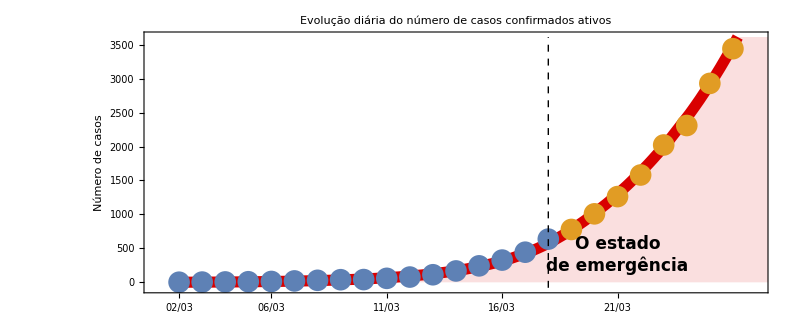

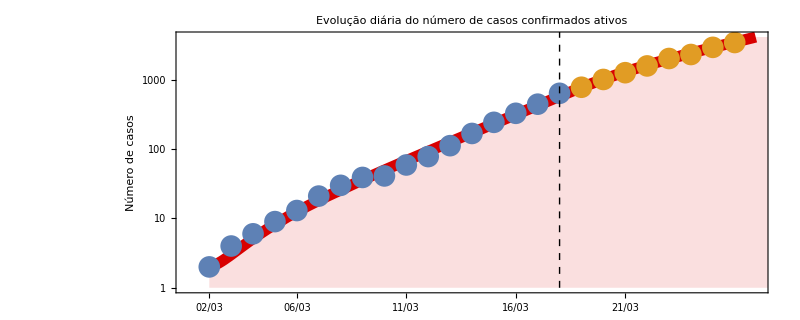

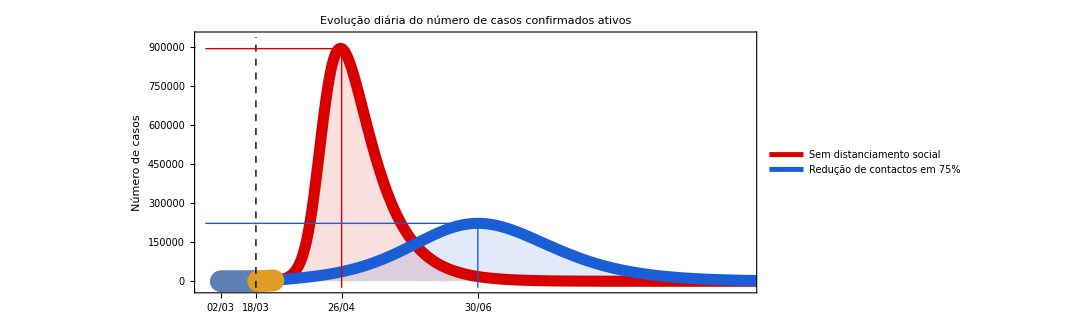

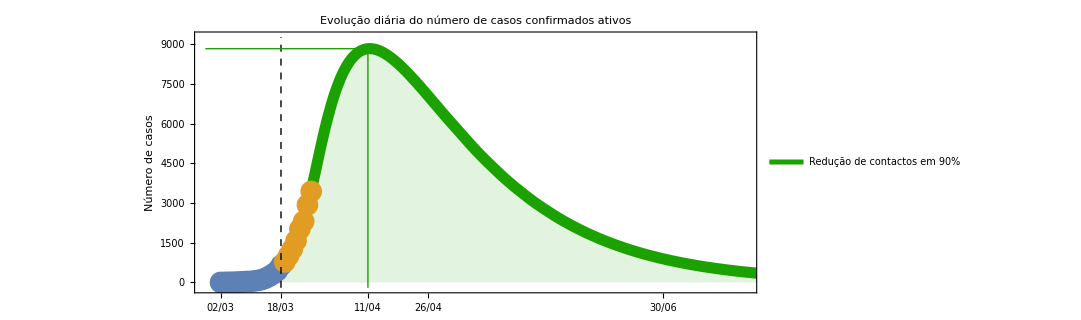

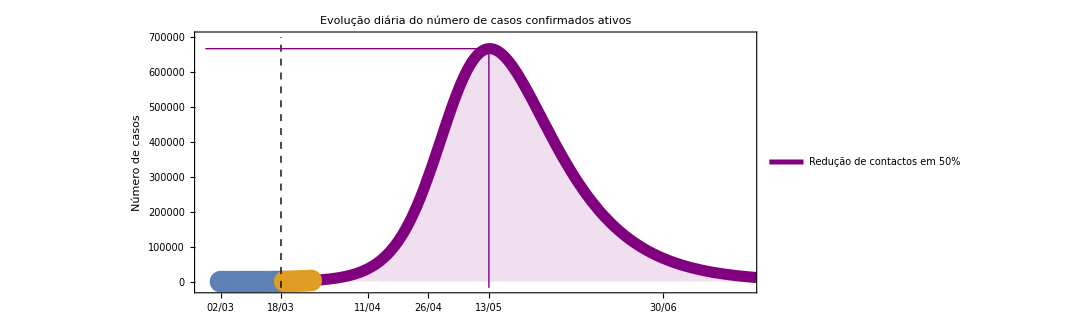

```mathematica
ymax=Last[DataAfter]⟦2⟧ 1.05;
ymin=-80;
tmax=Hoje+1/365;
tmin=Subscript[t, start]-1/365;
LabelBaseline="26/04";
Label75="30/06";
Label90="11/04";
Label50="13/05";


fig1=Table[Show[Plot[{Evaluate[IQ[t]/.solution[1,Parameters]]},{t,Subscript[t, start],Subscript[t, end]},AspectRatio->0.4,ImageSize->800,PlotRangePadding->None,Filling->Axis,PlotRange->{{tmin,tmax},{ymin,ymax}},AxesOrigin->{0,0},Frame-> {{True,False},{True,False}},FrameStyle->Directive[Black,17,Bold],PlotStyle->{Thickness[0.01],RGBColor[217/255,0,0]},FillingStyle->Directive[Opacity[0.125]],FrameLabel-> {{"Número de casos",None},{None,None}},PlotLabel->Style["Evolução diária do número de casos confirmados ativos",17,Black,Bold],
FrameTicks->{{Automatic,None},{{{1/365,"02/03"},{5/365,"06/03"},{10/365,"11/03"},{15/365,"16/03"},{20/365,"21/03"}},None}}],ListPlot[{DataBefore,DataAfter}],
Graphics[{Black,Dashed,Thick,Line[{{Emergencia,ymin},{Emergencia,ymax}}]}],
Graphics[{Red,Line[{{PeakTimingBaseline/365,ymin},{PeakTimingBaseline/365,PeakBaseline}}]}],Graphics[{Red,Line[{{tmin,PeakBaseline},{PeakTimingBaseline/365,PeakBaseline}}]}],
Graphics[Text[StyleForm["O estado\nde emergência",FontSize->17,Bold,FontColor-> Black],{20/365,400}]]],{i,1,Length[vars]}]⟦1⟧

ymax=Last[DataAfter]⟦2⟧ 1.2;
ymin=1;
tmax=Hoje+1/365;
tmin=Subscript[t, start]-1/365;

fig2=Table[Show[LogPlot[{Evaluate[IQ[t]/.solution[1,Parameters]]},{t,Subscript[t, start],Subscript[t, end]},AspectRatio->0.4,ImageSize->800,PlotRangePadding->None,Filling->Axis,PlotRange->{{tmin,tmax},{ymin,ymax}},AxesOrigin->{0,0},Frame-> {{True,False},{True,False}},FrameStyle->Directive[Black,17,Bold],PlotStyle->{Thickness[0.01],RGBColor[217/255,0,0]},FillingStyle->Directive[Opacity[0.125]],FrameLabel-> {{"Número de casos",None},{None,None}},PlotLabel->Style["Evolução diária do número de casos confirmados ativos",17,Black,Bold],
FrameTicks->{{Automatic,None},{{{1/365,"02/03"},{5/365,"06/03"},{10/365,"11/03"},{15/365,"16/03"},{20/365,"21/03"}},None}}],ListLogPlot[{DataBefore,DataAfter}],
Graphics[{Black,Dashed,Thick,Line[{{Emergencia,0},{Emergencia,ymax}}]}],
Graphics[{Red,Line[{{PeakTimingBaseline/365,ymin},{PeakTimingBaseline/365,PeakBaseline}}]}],Graphics[{Red,Line[{{tmin,PeakBaseline},{PeakTimingBaseline/365,PeakBaseline}}]}],
Graphics[Text[StyleForm["O estado\nde emergência",FontSize->17,Bold,FontColor-> Black],{20/365,400}]]],{i,1,Length[vars]}]⟦1⟧

ymax=PeakBaseline 1.05;
ymin=-25000;
tmax=240/365;
tmin=Subscript[t, start]-7/365;

fig3=Table[Show[Plot[{Evaluate[IQ[t]/.solution[1,Parameters]],Evaluate[IQ[t]/.solution[0.25,Parameters]]},{t,Subscript[t, start],Subscript[t, end]},AspectRatio->0.4,ImageSize->800,PlotRangePadding->None,Filling->Axis,PlotRange->{{tmin,tmax},{ymin,ymax}},AxesOrigin->{0,0},Frame-> {{True,False},{True,False}},FrameStyle->Directive[Black,17,Bold],PlotStyle->{{Thickness[0.01],RGBColor[217/255,0,0]},{Thickness[0.01],RGBColor[26/255,94/255,214/255]}},FillingStyle->Directive[Opacity[0.125]],FrameLabel-> {{"Número de casos",None},{None,None}},PlotLegends->Placed[{Table[Style[Row[{label}],Black,17,"Text",Bold],{label,{"Sem distanciamento social","Redução de contactos em 75%"}}]},{Scaled[{0,0.75}], {-1.25, 0.6}}],PlotLabel->Style["Evolução diária do número de casos confirmados ativos",17,Black,Bold],
FrameTicks->{{Automatic,None},{{{1/365,"02/03"},{PeakTimingBaseline/365,LabelBaseline},{Emergencia,"18/03"},{PeakTiming75/365,Label75}},None}}],ListPlot[{DataBefore,DataAfter}],
Graphics[{Black,Dashed,Thick,Line[{{Emergencia,ymin},{Emergencia,ymax}}]}],
Graphics[{RGBColor[217/255,0,0],Line[{{PeakTimingBaseline/365,ymin},{PeakTimingBaseline/365,PeakBaseline}}]}],Graphics[{RGBColor[217/255,0,0],Line[{{tmin,PeakBaseline},{PeakTimingBaseline/365,PeakBaseline}}]}],Graphics[{RGBColor[26/255,94/255,214/255],Line[{{PeakTiming75/365,ymin},{PeakTiming75/365,Peak75}}]}],Graphics[{RGBColor[26/255,94/255,214/255],Line[{{tmin,Peak75},{PeakTiming75/365,Peak75}}]}]],{i,1,Length[vars]}]⟦1⟧

ymax=Peak90 1.05;
ymin=-200;
tmax=140/365;
tmin=Subscript[t, start]-4/365;

fig4=Table[Show[Plot[{Evaluate[IQ[t]/.solution[0.1,Parameters]]},{t,Subscript[t, start],Subscript[t, end]},AspectRatio->0.4,ImageSize->800,PlotRangePadding->None,Filling->Axis,PlotRange->{{tmin,tmax},{ymin,ymax}},AxesOrigin->{0,0},Frame-> {{True,False},{True,False}},FrameStyle->Directive[Black,17,Bold],PlotStyle->{{Thickness[0.01],RGBColor[28/255,162/255,0]}},FillingStyle->Directive[Opacity[0.125]],FrameLabel-> {{"Número de casos",None},{None,None}},PlotLegends->Placed[{Table[Style[Row[{label}],Black,17,"Text",Bold],{label,{"Redução de contactos em 90%"}}]},{Scaled[{0,0.75}], {-1.25, 0.6}}],PlotLabel->Style["Evolução diária do número de casos confirmados ativos",17,Black,Bold],
FrameTicks->{{Automatic,None},{{{1/365,"02/03"},{PeakTiming90/365,Label90},{PeakTimingBaseline/365,LabelBaseline},{Emergencia,"18/03"},{PeakTiming75/365,Label75}},None}}],ListPlot[{DataBefore,DataAfter}],
Graphics[{Black,Dashed,Thick,Line[{{Emergencia,ymin},{Emergencia,ymax}}]}],
Graphics[{RGBColor[28/255,162/255,0],Line[{{PeakTiming90/365,ymin},{PeakTiming90/365,Peak90}}]}],Graphics[{RGBColor[28/255,162/255,0],Line[{{tmin,Peak90},{PeakTiming90/365,Peak90}}]}]],{i,1,Length[vars]}]⟦1⟧

Export[StringJoin["//Users//LynxGAV//Documents//Work//CoronaPortugal//Figures//Figure1",".pdf"],fig1];
Export[StringJoin["//Users//LynxGAV//Documents//Work//CoronaPortugal//Figures//Figure2",".pdf"],fig2];
Export[StringJoin["//Users//LynxGAV//Documents//Work//CoronaPortugal//Figures//Figure3",".pdf"],fig3];
Export[StringJoin["//Users//LynxGAV//Documents//Work//CoronaPortugal//Figures//Figure4",".pdf"],fig4];

ymax=Peak50 1.05;
ymin=-17500;
tmax=140/365;
tmin=Subscript[t, start]-4/365;

fig4=Table[Show[Plot[{Evaluate[IQ[t]/.solution[0.5,Parameters]]},{t,Subscript[t, start],Subscript[t, end]},AspectRatio->0.4,ImageSize->800,PlotRangePadding->None,Filling->Axis,PlotRange->{{tmin,tmax},{ymin,ymax}},AxesOrigin->{0,0},Frame-> {{True,False},{True,False}},FrameStyle->Directive[Black,17,Bold],PlotStyle->{{Thickness[0.01],Purple}},FillingStyle->Directive[Opacity[0.125]],FrameLabel-> {{"Número de casos",None},{None,None}},PlotLegends->Placed[{Table[Style[Row[{label}],Black,17,"Text",Bold],{label,{"Redução de contactos em 50%"}}]},{Scaled[{0,0.75}], {-1.49, 0.6}}],PlotLabel->Style["Evolução diária do número de casos confirmados ativos",17,Black,Bold],
FrameTicks->{{Automatic,None},{{{1/365,"02/03"},{PeakTiming90/365,Label90},{PeakTiming50/365,Label50},{PeakTimingBaseline/365,LabelBaseline},{Emergencia,"18/03"},{PeakTiming75/365,Label75}},None}}],ListPlot[{DataBefore,DataAfter}],
Graphics[{Black,Dashed,Thick,Line[{{Emergencia,ymin},{Emergencia,ymax}}]}],
Graphics[{Purple,Line[{{PeakTiming50/365,ymin},{PeakTiming50/365,Peak50}}]}],Graphics[{Purple,Line[{{tmin,Peak50},{PeakTiming50/365,Peak50}}]}]],{i,1,Length[vars]}]⟦1⟧

Export[StringJoin["//Users//LynxGAV//Documents//Work//CoronaPortugal//Figures//Figure5",".pdf"],fig5];
```